```mathematica
En={5,7,8,9,10,11,12}
```

{5,7,8,9,10,11,12}

```mathematica
W={1,1,1,1,1,1,1,1}*2
```

{2,2,2,2,2,2,2,2}

```mathematica
K[x_]:=-Sum[W[[i]]^2/(x-En[[i]]),{i,1,7}]
```

```mathematica
S[x_]:=(1+I K[x])/(1-I K[x])
```

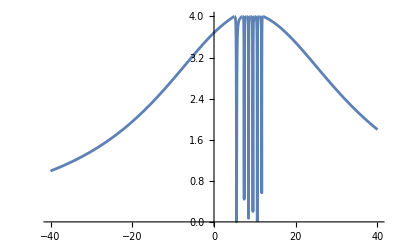

```mathematica
Plot[Abs[1-S[x]]^2,{x,-40,40},PlotRange->All]
```

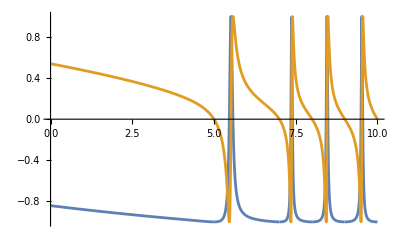

```mathematica
Plot[{Re[S[x]],Im[S[x]]},{x,0,10},PlotRange->All]
```